```mathematica
(*Solving Differential Eq.s By Using Laplace Transform.*)
(* IMPORTANT POINTS ABOUT LAPLACE TRANSFORM : 
1:-Laplace Transform can be used to Solve Linear Diff. Eq. for which initial conditions are given( Initial value Linear Problems).
Dep. variable is some unknown function of indep. variable.
2:- After Laplace Transform, A diff. Eq. is converted into an algebraic eq.
3:- Algebraic eq. can be solved to get Laplace Transform of unknown function f[t].
4:- Inverse Laplace Transform of the Solution of algebraic eq gives f[t].*)
```

(0.-0.0848189 ⅈ) ((0.-6.72956 ⅈ) 2.71828^(-0.810536 t)-(4.68671-3.36478 ⅈ) 2.71828^((0.905268-1.28374 ⅈ) t)+(4.68671+3.36478 ⅈ) 2.71828^((0.905268+1.28374 ⅈ) t))

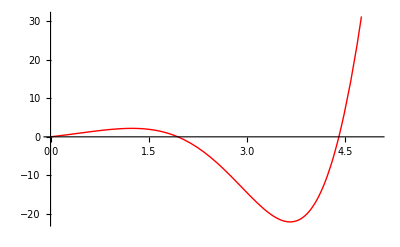

```mathematica
deq=f'''[t]-f''[t]+f'[t]+2f[t]==0;
initialCond={f''[0]->1,f'[0]->2,f[0]->0};
aeq=LaplaceTransform[deq,t,s] ; (* its solution will from 't' to  S-Variable.*)
(* Use initial cond. in algebraic eq. 'aeq'*)
aeq=aeq/.initialCond;
(*Solve the algebraic eq. to find LaplaceTransform[f[t],t,s] *)
Fs=LaplaceTransform[f[t],t,s]/.Solve[aeq,LaplaceTransform[f[t],t,s]][[1]];
sol=InverseLaplaceTransform[Fs,s,t]//N
Plot[sol,{t,0,5},PlotStyle->{{Red,Thick}}]
```

4 Cos[20 t]

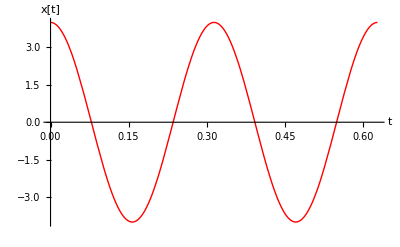

```mathematica
(*Example Problem: Solve x''[t]+w^2 x[t]==0, by using Laplace Transform method. The initial conditions are: x[0]->4,x'[0]->0.*)
Deq=x''[t]+w^2*x[t]==0;
initial={x[0]->4,x'[0]->0};
aleq=LaplaceTransform[Deq,t,s]/.initial;
fs=LaplaceTransform[x[t],t,s]/.Solve[aleq,LaplaceTransform[x[t],t,s]][[1]];
xt=InverseLaplaceTransform[fs,s,t]/.w->20
Plot[xt,{t,0,4*Pi/20},AxesLabel->{"t","x[t]"},PlotStyle->{{Red,Thick}}]
```